Parallelization in CIP 2.0: Parallelized Calculation

Minimal Model for the WDBC Data

This tutorial demonstrates new functions of CIP version 2.0 that complement the discussion in textbook

Achim Zielesny, From Curve Fitting to Machine Learning: An illustrative Guide to scientific Data Analysis and Computational Intelligence, Berlin 2011. (Springer: Intelligent Systems Reference Library, Volume 18).

CIP is available at http://www.gnwi.de.

```mathematica
Clear["Global`*"];
<<CIP`ExperimentalData`
<<CIP`DataTransformation`
<<CIP`Graphics`
<<CIP`Cluster`
<<CIP`MLR`
<<CIP`MPR`
<<CIP`Perceptron`
<<CIP`Utility`
```

Set number of kernels for parallelized calculation (0 is default and gives the number of processor cores available on the computer system):

```mathematica
Print["Time in s: ",AbsoluteTiming[numberOfLaunchedKernels=CIP`Utility`SetNumberOfParallelKernels[0]][[1]]]
```

Time in s: 3.20312

```mathematica
numberOfLaunchedKernels
```

16

The Wisconsin Diagnostic Breast Cancer (WDBC) data correlate 30 features of cell nuclei extracted from breast tumor tissue (as input) with the tumor type after diagnosis (as output), i.e. they map the cell nuclei features onto a diagnosed benign (class 1) or malignant (class 2) tumor type. Thus the WDBC data may be used to construct a class predictor that supports the crucial benign/malignant decision in tumor diagnosis. The WDBC classification data set is available via the CIP ExperimentalData package:

```mathematica
startTime=AbsoluteTime[];
```

```mathematica
classificationDataSet=CIP`ExperimentalData`GetWDBCClassificationDataSet[];
CIP`Graphics`ShowDataSetInfo[{"IoPairs","InputComponents","OutputComponents","ClassCount"},classificationDataSet]
```

Number of IO pairs = 569

Number of input components = 30

Number of output components = 2

Class 1 with 357 members

Class 2 with 212 members

A common task is to construct a minimal predictive model for a mapping of input features to the tumor type. A minimal model should consist of the smallest subset of input components/features that are necessary for a successful mapping in combination with the simplest type of predictive model function. As a start a linear MLR approach is chosen to determine important input components/features in a heuristic step-by-step fashion: In a first step all single input components/features are scanned for the one that leads to the best linear mapping from input to output with the best predictivity. Then this single best input component is fixed and the remaining input components are scanned for the next most relevant feature so that a pair of two relevant input components is achieved. This procedure is continued to get a relevant triple etc. This systematic evaluation does not necessarily lead to an optimum subset of relevant input components (i.e. those with the highest predictability) but may be regarded as a sensible heuristic choice. A true optimum input component subset search with e.g. an evolutionary search algorithm would be computationally far more demanding in general.

```mathematica
trainingAndTestSet={classificationDataSet,{}};
Print["Time in s: ",AbsoluteTiming[mlrInputComponentRelevanceListForClassification=CIP`MLR`GetMlrInputInclusionClass[trainingAndTestSet,UtilityOptionCalculationMode->"ParallelCalculation"]][[1]]]
```

Time in s: 67.65618

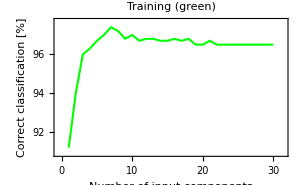

Input component list = {28,21,22,24,15,29,16,11,30,6,8,27,17,14,18,7,1,2,25,4,13,3,20,19,23,26,12,9,5,10}

```mathematica
CIP`MLR`ShowMlrInputRelevanceClass[mlrInputComponentRelevanceListForClassification]
```

The chosen step-by-step procedure achieves a success rate of more than 97% correct mappings for just 7 input components/features out of 30 with a linear MLR model. But it seems strange that the inclusion of more input components (i.e. more information) leads to a reduced number of correct predictions. This can be explained by the fact that a classification task is CIP-internally coded as a regression task where the RMSE values of the linear models drop constantly with an increased number of input components:

```mathematica
Print["Time in s: ",AbsoluteTiming[mlrInputComponentRelevanceListForRegression=CIP`MLR`GetMlrInputInclusionRegress[trainingAndTestSet,UtilityOptionCalculationMode->"ParallelCalculation"]][[1]]]
```

Time in s: 61.92181

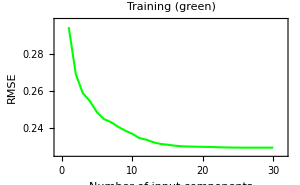

Input component list = {28,21,22,24,15,29,16,11,30,6,8,27,17,14,18,7,1,2,25,4,13,3,20,19,23,26,12,9,5,10}

```mathematica
CIP`MLR`ShowMlrInputRelevanceRegress[mlrInputComponentRelevanceListForRegression]
```

But this does not mean that the classification is necessarily improved because classification follows a winner-take-all principle (see textbook). The inputs of the WDBC data set may be reduced to the 7 detected most important/relevant features:

```mathematica
numberOfComponents=7;
inputComponentInclusionList=CIP`MLR`GetMlrClassRelevantComponents[mlrInputComponentRelevanceListForClassification,numberOfComponents]
```

{28,21,22,24,15,29,16}

```mathematica
reducedDataSet=CIP`DataTransformation`IncludeInputComponentsOfDataSet[classificationDataSet,inputComponentInclusionList];
```

To construct and validate a truly predictive model (not just a look-up-table-like mapping of the whole data) the reduced data set must be split into a training and a test set where the former is used to construct the model and the latter to validate it afterwards. To obtain training and test data that cover a similar input space with a similar spatial diversity (a desired feature to assure that the model is predictive on the whole range of inputs) in combination with a maximum predictive training set so called cluster representatives are evaluated in a first step (see textbook). These representatives are then refined by an iterative procedure that exchanges data between training and test set that belong to the same cluster. The latter constraint assures that the input data of training and test set maintain a similar spatial diversity. A single iteration determines the test set I/O pair with the largest deviation between data and model. This I/O pair is then transferred to the training set while the best predicted I/O pair of the same cluster in the training set is transferred to the test set in exchange. Oscillations during the refinement steps are suppressed by blacklisting exchanged I/O pairs. The training fraction is chosen to be 50% which means that 50% of the whole data set are used for training and the other 50% for validation which is a standard and convincing split if it succeeds (note that there is no parallel calculation option available for GetMlrTrainOptimization since each optimization step depends on the previous one so parallelization does not lead to improved performance):

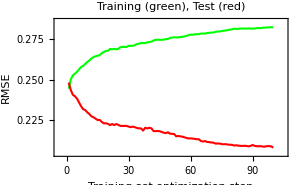

```mathematica
trainingFraction=0.50;
numberOfTrainingSetOptimizationSteps=100;
blackListLength=20;
mlrTrainOptimization=CIP`MLR`GetMlrTrainOptimization[reducedDataSet,trainingFraction,numberOfTrainingSetOptimizationSteps,UtilityOptionBlackListLength -> blackListLength];
CIP`MLR`ShowMlrTrainOptimization[mlrTrainOptimization]
```

The best training/test data combination with a minimum deviation in predictivity for a linear model is extracted from the analysis procedure

```mathematica
bestOptimization="MinimumDeviation";
Print["Time in s: ",AbsoluteTiming[bestClassificationStep=CIP`MLR`GetBestMlrClassOptimization[mlrTrainOptimization,UtilityOptionBestOptimization->bestOptimization,UtilityOptionCalculationMode->"ParallelCalculation"]][[1]]]
```

Time in s: 11.18749

```mathematica
bestClassificationStep
```

3

and checked:

```mathematica
optimizedTrainingAndTestSetList=mlrTrainOptimization[[3]];
optimizedTrainingAndTestSet=optimizedTrainingAndTestSetList[[bestClassificationStep]];
optimizedMlrInfoList=mlrTrainOptimization[[4]];
optimizedMlrInfo=optimizedMlrInfoList[[bestClassificationStep]];
CIP`MLR`ShowMlrClassificationResult[{"CorrectClassification"},optimizedTrainingAndTestSet,optimizedMlrInfo]
```

Training Set:

96.5% correct classifications

Test Set:

96.8% correct classifications

A correct classification rate of over 96% is achieved and validated with the test data. It may be interesting to know if non-linear methods are able to improve this result. A Multiple Polynomial Regression (MPR) approach with a polynomial order of 2 may be regarded as the first moderate step into non-linearity.

```mathematica
polynomialOrder=2;
```

If the procedure from above is repeated

```mathematica
trainingAndTestSet={classificationDataSet,{}};
numberOfInclusionsPerStepList=Table[1,{15}];
polynomialOrder=2;
Print["Time in s: ",AbsoluteTiming[mprInputComponentRelevanceListForClassification=CIP`MPR`GetMprInputInclusionClass[trainingAndTestSet,polynomialOrder,UtilityOptionInclusionsPerStep->numberOfInclusionsPerStepList,UtilityOptionCalculationMode->"ParallelCalculation"]][[1]]]
```

Time in s: 38.09371

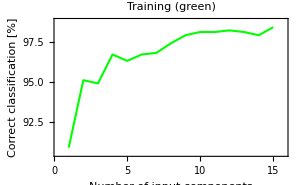

Input component list = {24,28,21,22,25,11,6,14,29,7,17,30,18,2,26}

```mathematica
CIP`MPR`ShowMprInputRelevanceClass[mprInputComponentRelevanceListForClassification]
```

it becomes obvious that only 4 input components are necessary to reach the 97% correct classification region. If again the whole data are split 50:50 into a training and a test set and optimized in the manner sketched above

```mathematica
numberOfComponents=4;
inputComponentInclusionList=CIP`MPR`GetMprClassRelevantComponents[mprInputComponentRelevanceListForClassification,numberOfComponents]
```

{24,28,21,22}

```mathematica
reducedDataSet=CIP`DataTransformation`IncludeInputComponentsOfDataSet[classificationDataSet,inputComponentInclusionList];
```

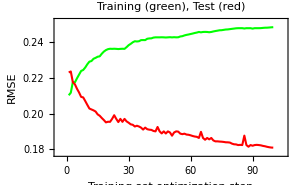

```mathematica
trainingFraction=0.50;
numberOfTrainingSetOptimizationSteps=100;
blackListLength=20;
mprTrainOptimization=CIP`MPR`GetMprTrainOptimization[reducedDataSet,polynomialOrder,trainingFraction,numberOfTrainingSetOptimizationSteps,UtilityOptionBlackListLength -> blackListLength];
CIP`MPR`ShowMprTrainOptimization[mprTrainOptimization]
```

```mathematica
bestOptimization="MinimumDeviation";
Print["Time in s: ",AbsoluteTiming[bestClassificationStep=CIP`MPR`GetBestMprClassOptimization[mprTrainOptimization,UtilityOptionBestOptimization->bestOptimization,UtilityOptionCalculationMode->"ParallelCalculation"]][[1]]]
```

Time in s: 10.29686

```mathematica
bestClassificationStep
```

3

```mathematica
optimizedTrainingAndTestSetList=mprTrainOptimization[[3]];
optimizedTrainingAndTestSet=optimizedTrainingAndTestSetList[[bestClassificationStep]];
optimizedMprInfoList=mprTrainOptimization[[4]];
optimizedMprInfo=optimizedMprInfoList[[bestClassificationStep]];
CIP`MPR`ShowMprClassificationResult[{"CorrectClassification"},optimizedTrainingAndTestSet,optimizedMprInfo]
```

Training Set:

96.1% correct classifications

Test Set:

96.5% correct classifications

again a correct classification rate of over 96% is achieved and validated - but now with only 4 input components. If 10 input components are chosen

```mathematica
numberOfComponents=10;
inputComponentInclusionList=CIP`MPR`GetMprClassRelevantComponents[mprInputComponentRelevanceListForClassification,numberOfComponents]
```

{24,28,21,22,25,11,6,14,29,7}

```mathematica
reducedDataSet=CIP`DataTransformation`IncludeInputComponentsOfDataSet[classificationDataSet,inputComponentInclusionList];
```

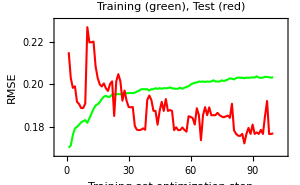

```mathematica
trainingFraction=0.50;
numberOfTrainingSetOptimizationSteps=100;
blackListLength=20;
mprTrainOptimization=CIP`MPR`GetMprTrainOptimization[reducedDataSet,polynomialOrder,trainingFraction,numberOfTrainingSetOptimizationSteps,UtilityOptionBlackListLength -> blackListLength];
CIP`MPR`ShowMprTrainOptimization[mprTrainOptimization]
```

```mathematica
bestOptimization="MinimumDeviation";
Print["Time in s: ",AbsoluteTiming[bestClassificationStep=CIP`MPR`GetBestMprClassOptimization[mprTrainOptimization,UtilityOptionBestOptimization->bestOptimization,UtilityOptionCalculationMode->"ParallelCalculation"]][[1]]]
```

Time in s: 14.67187

```mathematica
bestClassificationStep
```

3

```mathematica
optimizedTrainingAndTestSetList=mprTrainOptimization[[3]];
optimizedTrainingAndTestSet=optimizedTrainingAndTestSetList[[bestClassificationStep]];
optimizedMprInfoList=mprTrainOptimization[[4]];
optimizedMprInfo=optimizedMprInfoList[[bestClassificationStep]];
CIP`MPR`ShowMprClassificationResult[{"CorrectClassification"},optimizedTrainingAndTestSet,optimizedMprInfo]
```

Training Set:

97.5% correct classifications

Test Set:

97.5% correct classifications

the correct classification rate may be improved for another percent. Advancing to a polynomial order of 3

```mathematica
polynomialOrder=3;
```

and repeating the whole procedure

```mathematica
trainingAndTestSet={classificationDataSet,{}};
numberOfInclusionsPerStepList=Table[1,{10}];
polynomialOrder=3;
Print["Time in s: ",AbsoluteTiming[mprInputComponentRelevanceListForClassification=CIP`MPR`GetMprInputInclusionClass[trainingAndTestSet,polynomialOrder,UtilityOptionInclusionsPerStep->numberOfInclusionsPerStepList,UtilityOptionCalculationMode->"ParallelCalculation"]][[1]]]
```

Time in s: 32.40621

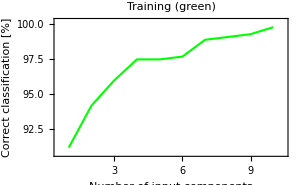

Input component list = {28,24,21,22,3,8,4,25,6,12}

```mathematica
CIP`MPR`ShowMprInputRelevanceClass[mprInputComponentRelevanceListForClassification]
```

with the now 4 detected most relevant input components

```mathematica
numberOfComponents=4;
inputComponentInclusionList=CIP`MPR`GetMprClassRelevantComponents[mprInputComponentRelevanceListForClassification,numberOfComponents]
```

{28,24,21,22}

```mathematica
reducedDataSet=CIP`DataTransformation`IncludeInputComponentsOfDataSet[classificationDataSet,inputComponentInclusionList];
```

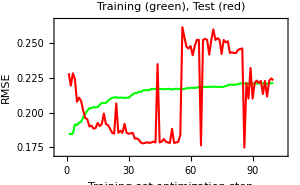

```mathematica
trainingFraction=0.50;
numberOfTrainingSetOptimizationSteps=100;
blackListLength=20;
mprTrainOptimization=CIP`MPR`GetMprTrainOptimization[reducedDataSet,polynomialOrder,trainingFraction,numberOfTrainingSetOptimizationSteps,UtilityOptionBlackListLength -> blackListLength];
CIP`MPR`ShowMprTrainOptimization[mprTrainOptimization]
```

```mathematica
bestOptimization="MinimumDeviation";
Print["Time in s: ",AbsoluteTiming[bestClassificationStep=CIP`MPR`GetBestMprClassOptimization[mprTrainOptimization,UtilityOptionBestOptimization->bestOptimization,UtilityOptionCalculationMode->"ParallelCalculation"]][[1]]]
```

Time in s: 10.82812

```mathematica
bestClassificationStep
```

4

```mathematica
optimizedTrainingAndTestSetList=mprTrainOptimization[[3]];
optimizedTrainingAndTestSet=optimizedTrainingAndTestSetList[[bestClassificationStep]];
optimizedMprInfoList=mprTrainOptimization[[4]];
optimizedMprInfo=optimizedMprInfoList[[bestClassificationStep]];
CIP`MPR`ShowMprClassificationResult[{"CorrectClassification"},optimizedTrainingAndTestSet,optimizedMprInfo]
```

Training Set:

96.8% correct classifications

Test Set:

96.8% correct classifications

leads to correct validated classification rate near 97% and using the 7 most relevant features

```mathematica
numberOfComponents=7;
inputComponentInclusionList=CIP`MPR`GetMprClassRelevantComponents[mprInputComponentRelevanceListForClassification,numberOfComponents]
```

{28,24,21,22,3,8,4}

```mathematica
reducedDataSet=CIP`DataTransformation`IncludeInputComponentsOfDataSet[classificationDataSet,inputComponentInclusionList];
```

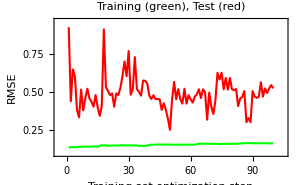

```mathematica
trainingFraction=0.50;
numberOfTrainingSetOptimizationSteps=100;
blackListLength=20;
mprTrainOptimization=CIP`MPR`GetMprTrainOptimization[reducedDataSet,polynomialOrder,trainingFraction,numberOfTrainingSetOptimizationSteps,UtilityOptionBlackListLength -> blackListLength];
CIP`MPR`ShowMprTrainOptimization[mprTrainOptimization]
```

```mathematica
bestOptimization="MinimumDeviation";
Print["Time in s: ",AbsoluteTiming[bestClassificationStep=CIP`MPR`GetBestMprClassOptimization[mprTrainOptimization,UtilityOptionBestOptimization->bestOptimization,UtilityOptionCalculationMode->"ParallelCalculation"]][[1]]]
```

Time in s: 27.68747

```mathematica
bestClassificationStep
```

88

```mathematica
optimizedTrainingAndTestSetList=mprTrainOptimization[[3]];
optimizedTrainingAndTestSet=optimizedTrainingAndTestSetList[[bestClassificationStep]];
optimizedMprInfoList=mprTrainOptimization[[4]];
optimizedMprInfo=optimizedMprInfoList[[bestClassificationStep]];
CIP`MPR`ShowMprClassificationResult[{"CorrectClassification"},optimizedTrainingAndTestSet,optimizedMprInfo]
```

Training Set:

97.5% correct classifications

Test Set:

97.5% correct classifications

achieved a correct validated classification rate over 97%. A further increase of the number of detected most relevant input components e.g. to 10

```mathematica
numberOfComponents=10;
inputComponentInclusionList=CIP`MPR`GetMprClassRelevantComponents[mprInputComponentRelevanceListForClassification,numberOfComponents]
```

{28,24,21,22,3,8,4,25,6,12}

```mathematica
reducedDataSet=CIP`DataTransformation`IncludeInputComponentsOfDataSet[classificationDataSet,inputComponentInclusionList];
```

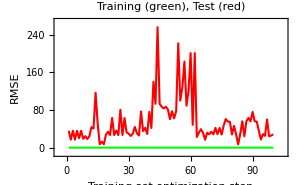

```mathematica
trainingFraction=0.50;
numberOfTrainingSetOptimizationSteps=100;
blackListLength=20;
mprTrainOptimization=CIP`MPR`GetMprTrainOptimization[reducedDataSet,polynomialOrder,trainingFraction,numberOfTrainingSetOptimizationSteps,UtilityOptionBlackListLength -> blackListLength];
CIP`MPR`ShowMprTrainOptimization[mprTrainOptimization]
```

```mathematica
bestOptimization="MinimumDeviation";
Print["Time in s: ",AbsoluteTiming[bestClassificationStep=CIP`MPR`GetBestMprClassOptimization[mprTrainOptimization,UtilityOptionBestOptimization->bestOptimization,UtilityOptionCalculationMode->"ParallelCalculation"]][[1]]]
```

Time in s: 40.40621

```mathematica
bestClassificationStep
```

64

```mathematica
optimizedTrainingAndTestSetList=mprTrainOptimization[[3]];
optimizedTrainingAndTestSet=optimizedTrainingAndTestSetList[[bestClassificationStep]];
optimizedMprInfoList=mprTrainOptimization[[4]];
optimizedMprInfo=optimizedMprInfoList[[bestClassificationStep]];
CIP`MPR`ShowMprClassificationResult[{"CorrectClassification"},optimizedTrainingAndTestSet,optimizedMprInfo]
```

Training Set:

100.% correct classifications

Test Set:

68.1% correct classifications

does not improve the predictivity of the model but results in an unwanted overfitting with a perfect prediction of the training data but only a poor predictivity of the test data due to the increased number of internal fit parameters. Finally a non-linear perceptron-type neural network may be investigated with a small number of 2 hidden neurons:

```mathematica
numberOfHiddenNeurons=2;
```

A scan of input component relevance

```mathematica
trainingAndTestSet={classificationDataSet,{}};
numberOfInclusionsPerStepList=Table[1,{10}];
Print["Time in hours: ",AbsoluteTiming[perceptronInputComponentRelevanceListForClassification=CIP`Perceptron`GetPerceptronInputInclusionClass[trainingAndTestSet,numberOfHiddenNeurons,UtilityOptionInclusionsPerStep->numberOfInclusionsPerStepList,UtilityOptionCalculationMode->"ParallelCalculation"]][[1]]/3600.]
```

Time in hours: 30.4616

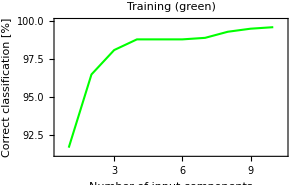

Input component list = {23,25,2,4,1,7,16,21,22,29}

```mathematica
CIP`Perceptron`ShowPerceptronInputRelevanceClass[perceptronInputComponentRelevanceListForClassification]
```

shows an already high predictivity for only 4 features

```mathematica
numberOfComponents=4;
inputComponentInclusionList=CIP`Perceptron`GetPerceptronClassRelevantComponents[perceptronInputComponentRelevanceListForClassification,numberOfComponents]
```

{23,25,2,4}

```mathematica
reducedDataSet=CIP`DataTransformation`IncludeInputComponentsOfDataSet[classificationDataSet,inputComponentInclusionList];
```

```mathematica
trainingFraction=0.50;
numberOfTrainingSetOptimizationSteps=100;
blackListLength=20;
Print["Time in hours: ",AbsoluteTiming[perceptronTrainOptimization=CIP`Perceptron`GetPerceptronTrainOptimization[reducedDataSet,numberOfHiddenNeurons,trainingFraction,numberOfTrainingSetOptimizationSteps,UtilityOptionBlackListLength -> blackListLength,UtilityOptionCalculationMode->"ParallelCalculation"]][[1]]/3600.]
```

Time in hours: 8.30118

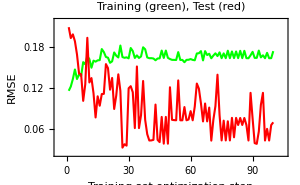

```mathematica
CIP`Perceptron`ShowPerceptronTrainOptimization[perceptronTrainOptimization]
```

```mathematica
bestOptimization="MinimumDeviation";
Print["Time in s: ",AbsoluteTiming[bestClassificationStep=CIP`Perceptron`GetBestPerceptronClassOptimization[perceptronTrainOptimization,UtilityOptionBestOptimization->bestOptimization,UtilityOptionCalculationMode->"ParallelCalculation"]][[1]]]
```

Time in s: 15.32812

```mathematica
bestClassificationStep
```

6

```mathematica
optimizedTrainingAndTestSetList=perceptronTrainOptimization[[3]];
optimizedTrainingAndTestSet=optimizedTrainingAndTestSetList[[bestClassificationStep]];
optimizedPerceptronInfoList=perceptronTrainOptimization[[4]];
optimizedPerceptronInfo=optimizedPerceptronInfoList[[bestClassificationStep]];
CIP`Perceptron`ShowPerceptronClassificationResult[{"CorrectClassification"},optimizedTrainingAndTestSet,optimizedPerceptronInfo]
```

Training Set:

97.9% correct classifications

Test Set:

97.9% correct classifications

with over 97% correct and validated predictivity. The use of the 6 most relevant input components

```mathematica
numberOfComponents=6;
inputComponentInclusionList=CIP`Perceptron`GetPerceptronClassRelevantComponents[perceptronInputComponentRelevanceListForClassification,numberOfComponents]
```

{23,25,2,4,1,7}

```mathematica
reducedDataSet=CIP`DataTransformation`IncludeInputComponentsOfDataSet[classificationDataSet,inputComponentInclusionList];
```

```mathematica
trainingFraction=0.50;
numberOfTrainingSetOptimizationSteps=100;
blackListLength=20;
Print["Time in hours: ",AbsoluteTiming[perceptronTrainOptimization=CIP`Perceptron`GetPerceptronTrainOptimization[reducedDataSet,numberOfHiddenNeurons,trainingFraction,numberOfTrainingSetOptimizationSteps,UtilityOptionBlackListLength -> blackListLength,UtilityOptionCalculationMode->"ParallelCalculation"]][[1]]/3600.]
```

Time in hours: 60.5693

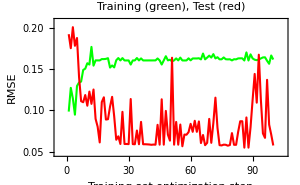

```mathematica
CIP`Perceptron`ShowPerceptronTrainOptimization[perceptronTrainOptimization]
```

```mathematica
bestOptimization="MinimumDeviation";
Print["Time in s: ",AbsoluteTiming[bestClassificationStep=CIP`Perceptron`GetBestPerceptronClassOptimization[perceptronTrainOptimization,UtilityOptionBestOptimization->bestOptimization,UtilityOptionCalculationMode->"ParallelCalculation"];
][[1]]
]
```

Time in s: 13.34374

```mathematica
bestClassificationStep
```

6

```mathematica
optimizedTrainingAndTestSetList=perceptronTrainOptimization[[3]];
optimizedTrainingAndTestSet=optimizedTrainingAndTestSetList[[bestClassificationStep]];
optimizedPerceptronInfoList=perceptronTrainOptimization[[4]];
optimizedPerceptronInfo=optimizedPerceptronInfoList[[bestClassificationStep]];
CIP`Perceptron`ShowPerceptronClassificationResult[{"CorrectClassification"},optimizedTrainingAndTestSet,optimizedPerceptronInfo]
```

Training Set:

98.6% correct classifications

Test Set:

98.6% correct classifications

results in an only minor improvement. A larger perceptron-type neural network with 3 hidden neurons

```mathematica
numberOfHiddenNeurons=3;
```

```mathematica
trainingAndTestSet={classificationDataSet,{}};
numberOfInclusionsPerStepList=Table[1,{10}];
Print["Time in hours: ",AbsoluteTiming[perceptronInputComponentRelevanceListForClassification=CIP`Perceptron`GetPerceptronInputInclusionClass[trainingAndTestSet,numberOfHiddenNeurons,UtilityOptionInclusionsPerStep->numberOfInclusionsPerStepList,UtilityOptionCalculationMode->"ParallelCalculation"]][[1]]/3600.]
```

Time in hours: 36.621

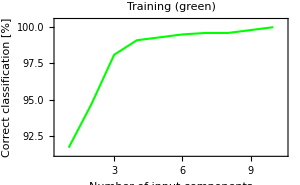

Input component list = {23,28,22,26,21,1,13,29,24,12}

```mathematica
CIP`Perceptron`ShowPerceptronInputRelevanceClass[perceptronInputComponentRelevanceListForClassification]
```

achieves for the best 4 input components

```mathematica
numberOfComponents=4;
inputComponentInclusionList=CIP`Perceptron`GetPerceptronClassRelevantComponents[perceptronInputComponentRelevanceListForClassification,numberOfComponents]
```

{23,28,22,26}

```mathematica
reducedDataSet=CIP`DataTransformation`IncludeInputComponentsOfDataSet[classificationDataSet,inputComponentInclusionList];
```

```mathematica
trainingFraction=0.50;
numberOfTrainingSetOptimizationSteps=100;
blackListLength=20;
Print["Time in hours: ",AbsoluteTiming[perceptronTrainOptimization=CIP`Perceptron`GetPerceptronTrainOptimization[reducedDataSet,numberOfHiddenNeurons,trainingFraction,numberOfTrainingSetOptimizationSteps,UtilityOptionBlackListLength -> blackListLength,UtilityOptionCalculationMode->"ParallelCalculation"]][[1]]/3600.]
```

Time in hours: 15.4022

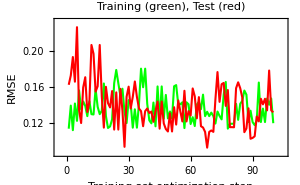

```mathematica
CIP`Perceptron`ShowPerceptronTrainOptimization[perceptronTrainOptimization]
```

```mathematica
bestOptimization="MinimumDeviation";
Print["Time in s: ",AbsoluteTiming[bestClassificationStep=CIP`Perceptron`GetBestPerceptronClassOptimization[perceptronTrainOptimization,UtilityOptionBestOptimization->bestOptimization,UtilityOptionCalculationMode->"ParallelCalculation"]][[1]]]
```

Time in s: 15.1875

```mathematica
bestClassificationStep
```

8

```mathematica
optimizedTrainingAndTestSetList=perceptronTrainOptimization[[3]];
optimizedTrainingAndTestSet=optimizedTrainingAndTestSetList[[bestClassificationStep]];
optimizedPerceptronInfoList=perceptronTrainOptimization[[4]];
optimizedPerceptronInfo=optimizedPerceptronInfoList[[bestClassificationStep]];
CIP`Perceptron`ShowPerceptronClassificationResult[{"CorrectClassification"},optimizedTrainingAndTestSet,optimizedPerceptronInfo]
```

Training Set:

98.2% correct classifications

Test Set:

98.2% correct classifications

a correct predictivity rate of nearly 97% and with the 6 best input components

```mathematica
numberOfComponents=6;
inputComponentInclusionList=CIP`Perceptron`GetPerceptronClassRelevantComponents[perceptronInputComponentRelevanceListForClassification,numberOfComponents]
```

{23,28,22,26,21,1}

```mathematica
reducedDataSet=CIP`DataTransformation`IncludeInputComponentsOfDataSet[classificationDataSet,inputComponentInclusionList];
```

```mathematica
trainingFraction=0.50;
numberOfTrainingSetOptimizationSteps=100;
blackListLength=20;
Print["Time in hours: ",AbsoluteTiming[perceptronTrainOptimization=CIP`Perceptron`GetPerceptronTrainOptimization[reducedDataSet,numberOfHiddenNeurons,trainingFraction,numberOfTrainingSetOptimizationSteps,UtilityOptionBlackListLength -> blackListLength,UtilityOptionCalculationMode->"ParallelCalculation"]][[1]]/3600.]
```

Time in hours: 21.7773

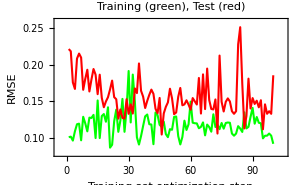

```mathematica
CIP`Perceptron`ShowPerceptronTrainOptimization[perceptronTrainOptimization]
```

```mathematica
bestOptimization="MinimumDeviation";
Print["Time in s: ",AbsoluteTiming[bestClassificationStep=CIP`Perceptron`GetBestPerceptronClassOptimization[perceptronTrainOptimization,UtilityOptionBestOptimization->bestOptimization,UtilityOptionCalculationMode->"ParallelCalculation"]][[1]]]
```

Time in s: 14.74999

```mathematica
bestClassificationStep
```

17

```mathematica
optimizedTrainingAndTestSetList=perceptronTrainOptimization[[3]];
optimizedTrainingAndTestSet=optimizedTrainingAndTestSetList[[bestClassificationStep]];
optimizedPerceptronInfoList=perceptronTrainOptimization[[4]];
optimizedPerceptronInfo=optimizedPerceptronInfoList[[bestClassificationStep]];
CIP`Perceptron`ShowPerceptronClassificationResult[{"CorrectClassification"},optimizedTrainingAndTestSet,optimizedPerceptronInfo]
```

Training Set:

97.9% correct classifications

Test Set:

97.9% correct classifications

a validated predictivity of over 98% is reached. A further increase of the number of hidden neurons may again lead to unwanted overfitting with a decreased predictivity.

```mathematica
Print["Total time in hours: ", (AbsoluteTime[]-startTime)/3600.]
```

Total time in hours: 173.419